```mathematica
ouNoisePath=Table[{t,t},{t,0,10,0.1}];
nf=Interpolation[ouNoisePath,InterpolationOrder->0];
ou[t_]:=nf[t]
```

```mathematica
ou[0.200000001]
```

0.3

```mathematica
data={{0,0},{1,2},{3,4},{4,2},{6,0}};
```

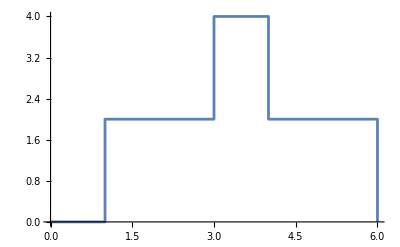

```mathematica
ListLinePlot[data,InterpolationOrder->0]
```